立即赋值与延迟赋值

在 Wolfram 语言中，有两种方法可以为某个对象赋值：立即赋值(=)，和延迟赋值(:=)。

在立即赋值中，当赋值完成后，就会立即计算该值，并且永远不会重新计算。在延迟赋值中，值的计算会被延迟，在每次请求值时再进行计算。

举一个简单的例子，考虑 value=RandomColor[ ] 与 value:=RandomColor[ ] 之间的区别。

在立即赋值(=)中，会立即生成一个随机颜色：

```mathematica
value=RandomColor[ ]
```

RGBColor[0.5776360098335713, 0.16742506587239303, 0.23693496006313164]

每次你查询 value，都会得到相同的随机颜色：

```mathematica
value
```

RGBColor[0.5776360098335713, 0.16742506587239303, 0.23693496006313164]

在延迟赋值(:=)中，不会立即生成随机颜色：

```mathematica
value:=RandomColor[ ]
```

每次你查询 value，都会重新计算 RandomColor[ ]，生成一个新的随机颜色：

```mathematica
value
```

RGBColor[0.8431574152311205, 0.8848301850335125, 0.4749471491092443]

通常每次的颜色都会不同：

```mathematica
value
```

RGBColor[0.7127712074377826, 0.37013138983058824, 0.9880717025911983]

当你定义一个值的时候，如果某些对象还没有准备好，使用 := 是非常常见的。

即使 n 还没有一个值，你也可以为 circles 创建一个延迟赋值：

```mathematica
circles:=Graphics[Table[Circle[{x,0},x/2],{x,n}]]
```

给 n 一个值：

```mathematica
n=6
```

6

现在你可以查询 circles，将会使用你给 n 赋的值：

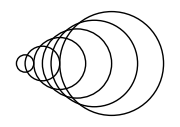

```mathematica
circles
```

延迟赋值的概念与我们讨论的用于部署网页的 Delayed 结构非常相似。在延迟赋值中，我们在需要使用它之前都不会计算值。同样地，当我们在进行 CloudDeploy 时使用 Delayed 后，我们在请求网页内容之前都不会进行计算。

延迟规则也有一个符号。x→rhs 会立即计算 rhs。但在延迟规则 x:>rhs(使用 :> 来输入)中，在每次请求 rhs 时都会被重新计算。

这是一个立即规则，RandomReal[ ] 的具体数值会立即被计算出来：

```mathematica
x->RandomReal[ ]
```

x→0.522293

你可以替换四个 x，但它们都是一样的：

```mathematica
{x,x,x,x}/.x->RandomReal[ ]
```

{0.821639,0.821639,0.821639,0.821639}

这是一个延迟规则，其中 RandomReal[ ] 的计算被延迟了：

```mathematica
x:>RandomReal[ ]
```

x:>RandomReal[ ]

当替换每个 x 时，RandomReal[ ] 会分别进行计算，给出四个不同的值：

```mathematica
{x,x,x,x}/.x:>RandomReal[ ]
```

{0.536115,0.84214,0.242933,0.514131}

词汇

x:=value |   | 延迟赋值，在每次请求 x 时才进行计算
x:>value |   | 延迟规则，每次遇到 x 时才进行计算

"共有 2 道习题" | "开始练习 »"

将 {x,x+1,x+2,x^2} 中的 x 替换为相同的 100 以内的随机整数。»

| 期望输出示例： |  
  | {97,98,99,9409} |

将 {x,x+1,x+2,x^2} 中的 x 替换为单独计算的 100 以内的随机整数。»

| 期望输出示例： |  
  | {100,3,38,7225} |

问&答

为什么不总是使用 :=？

因为除非有必要，否则不希望一直重新进行计算。只计算一次，然后反复使用其结果，这样会更有效率。

如何读 := 和 :>？

:= 通常读作“冒号等于”，有时也读作“延迟赋值”。:> 通常读作“冒号大于”，有时也读作“延迟规则”。

如果我在 x 尚未赋值时计算 x=x+1，会发生什么？

你会开始陷入一个无限循环，最终被系统终止。x={x} 也是同样的情况。

输入被标记为 In[n]:=，而输出为 Out[n]= 的意义是什么？

它表示输入被指派为 In[n]，输出被指派为 Out[n]。输入的 := 意味着赋值是延迟的，所以如果你要求 In[n] 时，结果将会被重新进行计算。

技术笔记

在 Wolfram 语言中，计算结果的过程通常被称为评估(evaluation，译者注：Mathematica 中的菜单都将 Evaluate 翻译为计算，因此，翻译过程中将 Calculate 以及 Evaluate 都翻译为计算，一般情况下不会造成混淆，如有特殊情况，会另外指出)，因为它涉及寻找对象的值。

Wolfram 语言有许多控制计算的方法。一个例子是函数 Hold，它将表达式维持在“保持”的形式，直到它被“释放”。

x=y 的内部形式是 Set[x,y]。x:=y 是 SetDelayed[x,y]。x:>y 是 RuleDelayed[x,y]。